```mathematica
Remove ["Global`*"]
```

Using DSolve function to solve for the coupled differential equations, eq1 & eq2, of two identical masses connected by three identical springs with the four initial conditions.

Define w0 = 1 for simplification.

```mathematica
w0 = 1
```

1

```mathematica
eq1 = x1''[t]+2 w0^2 x1[t]- w0^2 x2[t] == 0;
```

```mathematica
eq2 = x2''[t]+2 w0^2 x2[t]- w0^2 x1[t] == 0;
```

Solving for x1 & x2

```mathematica
sol = DSolve[{eq1,eq2,x1[0]==1, x1'[0]== x2[0]==x2'[0]==0},{ x1,x2},t]
```

{{x1→Function[{t},1/2 (Cos[t]+Cos[√3 t])],x2→Function[{t},1/2 (Cos[t]-Cos[√3 t])]}}

Simplifying the solutions for an easier expression to work with

```mathematica
sol1 = Simplify[x1[t] /. sol[[1]]]
```

1/2 (Cos[t]+Cos[√3 t])

```mathematica
sol2 = Simplify[x2[t] /. sol[[1]]]
```

1/2 (Cos[t]-Cos[√3 t])

Graph of motion of x1 & x2 with respect to time

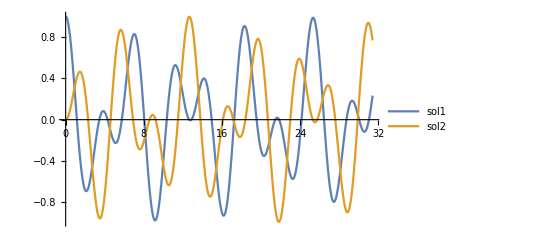

```mathematica
p1 = Plot[{sol1,sol2},{t,0,2Pi*5}, PlotLegends->"Expressions"]
```

Equations for x1 + x2 and x1 - x2

```mathematica
xm = sol1-sol2
```

1/2 (-Cos[t]+Cos[√3 t])+1/2 (Cos[t]+Cos[√3 t])

```mathematica
xp = sol1 + sol2
```

1/2 (Cos[t]-Cos[√3 t])+1/2 (Cos[t]+Cos[√3 t])

Using ListLinePlot to to make dashed lines indicating the expected periods corresponding to the eigenfrequencies

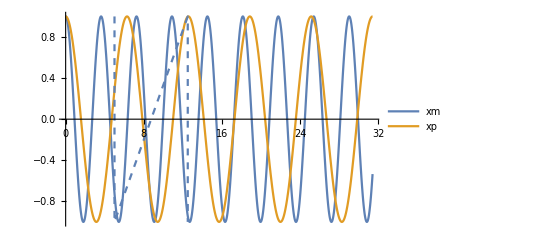

```mathematica
Show[Plot[{xm,xp},{t,0,5*2Pi}, PlotLegends->"Expressions"],
ListLinePlot[{{5,1},{5,-1},{12.5,1},{12.5,-1}}, PlotStyle->Dashed]]
```